```mathematica
Covariance
```

```mathematica
SetDirectory["Visual Studio Projects\\smmbp\\Background"];
Needs["MultivariateStatistics`"]
```

216

{{1.,0.0622084,-0.0633554,-0.0111874,-0.168569,0.192684,-0.313718,-0.00454761,-0.0380111,-0.172374,-0.274029,-0.363772,0.219283,-0.203034,-0.0402809,0.161212,0.231462,0.33342,-0.497215,-0.271517},{0.0622084,1.,0.0840683,0.154675,0.182885,0.100881,-0.0396387,-0.0132669,-0.26561,-0.148358,-0.147679,0.0158203,-0.0327232,-0.19405,-0.237787,-0.16407,-0.164387,-0.130137,0.257036,0.0228713},{-0.0633554,0.0840683,1.,0.486333,-0.122096,-0.042869,-0.114386,-0.174175,-0.255189,-0.198436,-0.189303,0.138506,0.19146,0.0190646,-0.224555,-0.0483997,0.0540535,-0.152384,0.032601,-0.117671},{-0.0111874,0.154675,0.486333,1.,-0.0456548,-0.0317952,-0.199989,-0.0986037,-0.353822,0.0224586,-0.156158,0.0446834,0.120557,0.199213,-0.309005,-0.109503,-0.0239527,-0.074215,-0.0617143,-0.132759},{-0.168569,0.182885,-0.122096,-0.0456548,1.,-0.0307544,-0.0158247,0.258841,-0.192314,0.231545,0.177603,-0.125746,-0.316173,-0.440907,-0.199885,-0.414424,-0.390817,-0.0458186,0.266475,0.342456},{0.192684,0.100881,-0.042869,-0.0317952,-0.0307544,1.,-0.15373,-0.119112,-0.0749651,-0.232572,-0.198442,-0.0159546,0.0524528,0.0267277,-0.110966,0.204835,0.0570011,-0.0982341,-0.16069,-0.12095},{-0.313718,-0.0396387,-0.114386,-0.199989,-0.0158247,-0.15373,1.,-0.348024,0.304757,-0.185708,-0.00202109,0.17391,-0.245147,-0.049952,0.372868,0.039976,-0.12376,-0.431091,0.0445735,0.162867},{-0.00454761,-0.0132669,-0.174175,-0.0986037,0.258841,-0.119112,-0.348024,1.,-0.140752,0.409264,0.29288,-0.286445,-0.157441,-0.304361,-0.320841,-0.290002,-0.177136,0.430032,0.0138959,-0.0720636},{-0.0380111,-0.26561,-0.255189,-0.353822,-0.192314,-0.0749651,0.304757,-0.140752,1.,-0.0939776,-0.0520733,-0.150363,-0.147199,-0.137084,0.65099,0.0207478,-0.157071,-0.192543,-0.244813,-0.0256351},{-0.172374,-0.148358,-0.198436,0.0224586,0.231545,-0.232572,-0.185708,0.409264,-0.0939776,1.,0.444361,-0.0829618,-0.205888,-0.00755973,-0.287163,-0.359063,-0.210977,0.28142,-0.0548854,-0.0545259},{-0.274029,-0.147679,-0.189303,-0.156158,0.177603,-0.198442,-0.00202109,0.29288,-0.0520733,0.444361,1.,0.0409076,-0.399273,-0.0268065,-0.0933812,-0.185803,-0.310634,-0.0342723,0.135762,0.0718251},{-0.363772,0.0158203,0.138506,0.0446834,-0.125746,-0.0159546,0.17391,-0.286445,-0.150363,-0.0829618,0.0409076,1.,-0.0358234,0.232829,-0.138407,0.103421,-0.0215341,-0.275549,0.16122,-0.0226213},{0.219283,-0.0327232,0.19146,0.120557,-0.316173,0.0524528,-0.245147,-0.157441,-0.147199,-0.205888,-0.399273,-0.0358234,1.,0.213287,-0.0941337,-0.017883,0.0919579,0.065473,-0.206413,-0.307187},{-0.203034,-0.19405,0.0190646,0.199213,-0.440907,0.0267277,-0.049952,-0.304361,-0.137084,-0.00755973,-0.0268065,0.232829,0.213287,1.,0.030945,0.21257,0.163856,-0.20211,-0.0663152,-0.230244},{-0.0402809,-0.237787,-0.224555,-0.309005,-0.199885,-0.110966,0.372868,-0.320841,0.65099,-0.287163,-0.0933812,-0.138407,-0.0941337,0.030945,1.,0.0810936,-0.169347,-0.349161,-0.198124,0.025584},{0.161212,-0.16407,-0.0483997,-0.109503,-0.414424,0.204835,0.039976,-0.290002,0.0207478,-0.359063,-0.185803,0.103421,-0.017883,0.21257,0.0810936,1.,0.536132,-0.0549447,-0.233694,-0.280071},{0.231462,-0.164387,0.0540535,-0.0239527,-0.390817,0.0570011,-0.12376,-0.177136,-0.157071,-0.210977,-0.310634,-0.0215341,0.0919579,0.163856,-0.169347,0.536132,1.,0.29443,-0.163994,-0.246203},{0.33342,-0.130137,-0.152384,-0.074215,-0.0458186,-0.0982341,-0.431091,0.430032,-0.192543,0.28142,-0.0342723,-0.275549,0.065473,-0.20211,-0.349161,-0.0549447,0.29443,1.,-0.153653,-0.205861},{-0.497215,0.257036,0.032601,-0.0617143,0.266475,-0.16069,0.0445735,0.0138959,-0.244813,-0.0548854,0.135762,0.16122,-0.206413,-0.0663152,-0.198124,-0.233694,-0.163994,-0.153653,1.,0.360395},{-0.271517,0.0228713,-0.117671,-0.132759,0.342456,-0.12095,0.162867,-0.0720636,-0.0256351,-0.0545259,0.0718251,-0.0226213,-0.307187,-0.230244,0.025584,-0.280071,-0.246203,-0.205861,0.360395,1.}}

{2.84495×10^-17,3.96384×10^-17,-4.98733×10^-17,5.49907×10^-17,5.47359×10^-17,7.92769×10^-17,-3.80772×10^-17,4.85723×10^-17,-1.14665×10^-16,3.0813×10^-17,5.77663×10^-17,-3.04444×10^-17,4.75314×10^-17,7.28584×10^-18,-4.58834×10^-17,2.29677×10^-16,-1.61156×10^-16,3.6646×10^-16,-1.58554×10^-16,-0.223607}

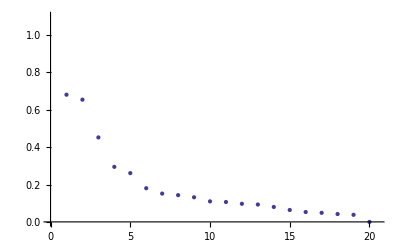

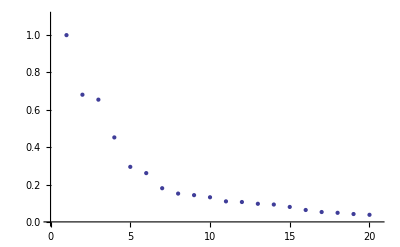

{{6.91547,-3.07161,0.134498,-0.741122,-0.280512,-1.51765,0.96567,0.606473,-0.0282073,0.798419,-0.914074,1.36445,-1.16558,1.39508,-0.873034,-1.13304,-1.29825,-3.00122,3.17127,-0.327026},{-3.07161,13.7503,-0.0645986,-2.75382,-1.02198,-1.98608,-1.66361,-1.03409,0.36918,-0.0766286,0.966599,-1.23425,-0.216683,0.724222,0.225913,0.156015,0.776227,1.12385,-4.4913,0.522308},{0.134498,-0.0645986,9.92078,-6.14844,0.243021,-0.147163,0.00977856,-0.123953,-0.187222,0.966629,-0.810718,-1.55781,-1.45081,1.75685,-0.0144607,0.366269,-1.97427,0.93299,-0.979496,0.128143},{-0.741122,-2.75382,-6.14844,13.4402,-0.977439,0.201546,-0.0385638,0.0468859,0.600332,-1.89172,1.04385,0.223201,0.265773,-3.84938,0.551713,0.00650683,0.65217,-0.281442,1.07555,-0.425746},{-0.280512,-1.02198,0.243021,-0.977439,7.38531,-1.8109,-0.765937,-1.04353,1.1379,-2.49189,-0.173684,0.028187,0.256708,2.54584,-0.548605,0.491782,0.818932,0.461793,-1.47752,-1.77748},{-1.51765,-1.98608,-0.147163,0.201546,-1.8109,10.3631,0.603879,-0.393482,-1.30848,0.88667,0.113314,-0.791078,-0.408464,-1.79181,0.823807,-2.57668,0.140822,0.538159,0.501722,-0.441269},{0.96567,-1.66361,0.00977856,-0.0385638,-0.765937,0.603879,7.92725,0.902527,-1.41582,-0.332979,-0.703758,-1.69543,0.136163,0.522459,-1.64829,-0.793579,-1.32672,0.987828,0.236112,-0.906986},{0.606473,-1.03409,-0.123953,0.0468859,-1.04353,-0.393482,0.902527,6.87697,-0.688223,-1.44143,-2.13057,1.10937,-0.163761,0.77302,0.475514,-0.279472,0.804404,-3.46929,-0.22464,0.397274},{-0.0282073,0.36918,-0.187222,0.600332,1.1379,-1.30848,-1.41582,-0.688223,8.20564,-2.10575,0.294595,-0.245735,-0.0506182,1.54952,-4.65623,-0.333372,0.0401979,-0.217496,0.261087,-0.221304},{0.798419,-0.0766286,0.966629,-1.89172,-2.49189,0.88667,-0.332979,-1.44143,-2.10575,12.8741,-4.57317,-0.550187,0.166357,-3.05821,1.58177,2.21859,-0.277523,-3.71575,1.79396,0.22875},{-0.914074,0.966599,-0.810718,1.04385,-0.173684,0.113314,-0.703758,-2.13057,0.294595,-4.57317,10.6408,-1.24816,1.50715,-1.48783,-0.530066,-1.5673,2.09544,0.593666,-1.74984,-0.366248},{1.36445,-1.23425,-1.55781,0.223201,0.028187,-0.791078,-1.69543,1.10937,-0.245735,-0.550187,-1.24816,9.48437,-0.463249,-1.66276,1.00651,-1.83857,0.376625,-0.383557,-0.771761,-0.150163},{-1.16558,-0.216683,-1.45081,0.265773,0.256708,-0.408464,0.136163,-0.163761,-0.0506182,0.166357,1.50715,-0.463249,4.36573,-2.05647,-0.171046,0.829007,0.338205,-0.916275,-0.230848,0.428717},{1.39508,0.724222,1.75685,-3.84938,2.54584,-1.79181,0.522459,0.77302,1.54952,-3.05821,-1.48783,-1.66276,-2.05647,10.9578,-2.14245,-1.45392,-2.24111,1.41014,-1.07861,0.187608},{-0.873034,0.225913,-0.0144607,0.551713,-0.548605,0.823807,-1.64829,0.475514,-4.65623,1.58177,-0.530066,1.00651,-0.171046,-2.14245,6.71406,-0.838897,1.15114,0.372518,0.0771002,-0.556985},{-1.13304,0.156015,0.366269,0.00650683,0.491782,-2.57668,-0.793579,-0.279472,-0.333372,2.21859,-1.5673,-1.83857,0.829007,-1.45392,-0.838897,12.959,-7.23607,0.717385,0.353201,0.953111},{-1.29825,0.776227,-1.97427,0.65217,0.818932,0.140822,-1.32672,0.804404,0.0401979,-0.277523,2.09544,0.376625,0.338205,-2.24111,1.15114,-7.23607,15.4279,-5.40604,-1.33051,-0.531553},{-3.00122,1.12385,0.93299,-0.281442,0.461793,0.538159,0.987828,-3.46929,-0.217496,-3.71575,0.593666,-0.383557,-0.916275,1.41014,0.372518,0.717385,-5.40604,12.843,-1.53249,-0.057765},{3.17127,-4.4913,-0.979496,1.07555,-1.47752,0.501722,0.236112,-0.22464,0.261087,1.79396,-1.74984,-0.771761,-0.230848,-1.07861,0.0771002,0.353201,-1.33051,-1.53249,9.89327,-2.49625},{-0.327026,0.522308,0.128143,-0.425746,-1.77748,-0.441269,-0.906986,0.397274,-0.221304,0.22875,-0.366248,-0.150163,0.428717,0.187608,-0.556985,0.953111,-0.531553,-0.057765,-2.49625,6.41286}}

```mathematica
libfile = Import["FormattedCombinatorials_log_ic50.txt","TSV"];
 Rows = Dimensions[libfile][[1]]-1
libvals = libfile[[2;;1+ Rows,3;;22]];
rowmeans = Mean[Transpose[libvals]];
For[row = 1, row≤Rows, row++, libvals[[row, All]]-=rowmeans[[row]];]
(*By normalizing all rows by their rowmeans, the libvals can be interpreted as deviations of an amino acid from the mean interaction. This makes different rows comparable *) 
Covar = Covariance[libvals];
CC = Correlation[libvals]
{coeigenval,coeigenvec}= Eigensystem[Covar];
Mean[Transpose[coeigenvec]]
ListPlot[coeigenval, PlotRange->{{0,20.5},{0,1.1}}]
(*All Eigenvectors have sum = zero, as they are relative differences between amino acids due to the normalization. *)
(*This also means that there is an implied Eigenvector (1,1,1,1...),  of coordinated movements of all amino acids. *)
Max[Covar - Transpose[Covar]];
Covar =(Covar + Transpose[Covar]) / 2.0 + .05 ;
{coeigenval2,coeigenvec2}= Eigensystem[Covar];
ListPlot[coeigenval2, PlotRange->{{0,20.5},{0,1.1}}]
(*Adding the transpose ensures exact symmetry, (which due to rounding errors  apparently isn't there even though it should.*) 
(*Adding a constant increases only the Eigenvalue of the Eigenvector (1,1,1,1,1...) to ~ 1.0.  The same effect ccould be achieved by repeating the libvals dataset while adding an offset to all libvals in the repeat. No other eigenvectors are affected. What constant is added is irrelevant for the result. *)
InvCovar = Inverse[Covar] ;
InvCovar = (InvCovar + Transpose[InvCovar])/2.0
Export["InverseCovariance.txt",InvCovar,"TSV"];
(* Again, the adding of transpose is to reach perfect symmetry, which should be but isn't the case for the mathematica output (just a difference of 10^-18..., but not nice) *)
```

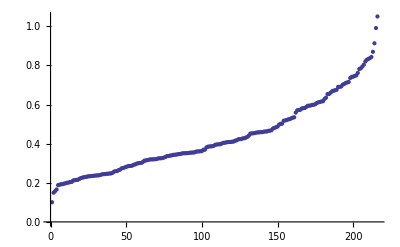

{0.380629,0.144878}

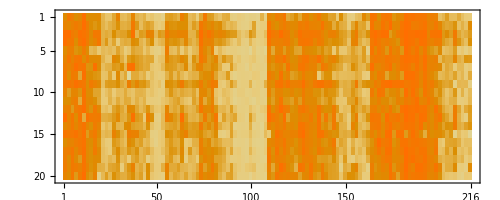

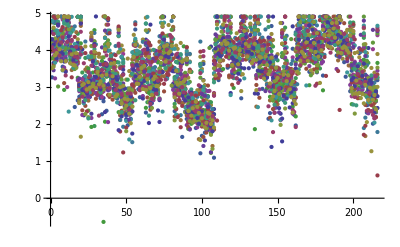

{1.,1.}

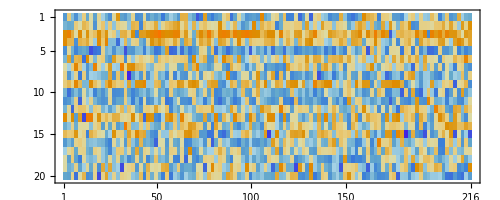

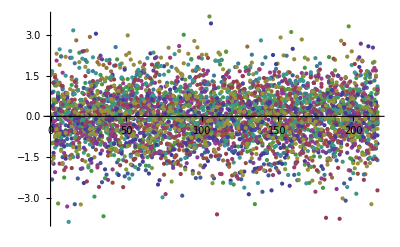

{{1.,0.0888264,-0.0104129,0.0528164,-0.193373,0.159943,-0.233017,-0.116208,-0.0799657,-0.222531,-0.271753,-0.157297,0.25165,-0.102583,-0.0364955,0.101136,0.155257,0.170886,-0.411154,-0.217941},{0.0888264,1.,-0.0640271,0.138243,0.090086,0.0393045,-0.00749852,-0.0454405,-0.202254,-0.0211799,-0.0822914,0.0281163,-0.101872,-0.110265,-0.151553,-0.12679,-0.152326,-0.0794228,0.0871998,-0.0557119},{-0.0104129,-0.0640271,1.,0.368353,-0.0556114,-0.034687,-0.195651,-0.0619093,-0.197153,-0.133427,-0.0489063,0.0336483,0.053669,-0.0833311,-0.31359,-0.082958,0.0377534,-0.0376489,0.0255002,-0.146919},{0.0528164,0.138243,0.368353,1.,-0.0221582,-0.0364776,-0.238588,-0.0880053,-0.393739,0.0220523,-0.203919,0.0023729,0.103518,0.137557,-0.323664,-0.0870727,-0.0138359,0.00692138,-0.11215,-0.0368276},{-0.193373,0.090086,-0.0556114,-0.0221582,1.,0.0454596,0.0167613,0.0879249,-0.127128,0.0470863,-0.0178843,-0.015054,-0.207892,-0.326444,-0.17259,-0.230819,-0.201946,-0.138794,0.207552,0.228555},{0.159943,0.0393045,-0.034687,-0.0364776,0.0454596,1.,-0.0875918,-0.0684138,-0.0178933,-0.194214,-0.160642,-0.0902886,0.000431426,-0.125581,-0.00830399,0.142136,-0.054596,-0.121095,-0.201838,-0.111722},{-0.233017,-0.00749852,-0.195651,-0.238588,0.0167613,-0.0875918,1.,-0.0943403,0.24282,-0.11857,0.0181189,0.0325383,-0.179748,-0.132502,0.256333,-0.0427813,-0.0852651,-0.257781,-0.0848795,0.0436826},{-0.116208,-0.0454405,-0.0619093,-0.0880053,0.0879249,-0.0684138,-0.0943403,1.,0.00849129,0.240982,0.180008,-0.177016,-0.193567,-0.253645,-0.225235,-0.214503,-0.129153,0.316437,0.00792893,-0.0907177},{-0.0799657,-0.202254,-0.197153,-0.393739,-0.127128,-0.0178933,0.24282,0.00849129,1.,-0.0046577,0.0483657,-0.169898,-0.171193,-0.190714,0.529607,-0.0387511,-0.136324,-0.144994,-0.180141,-0.0800943},{-0.222531,-0.0211799,-0.133427,0.0220523,0.0470863,-0.194214,-0.11857,0.240982,-0.0046577,1.,0.247751,-0.00547572,-0.115392,0.0572297,-0.164142,-0.318108,-0.228605,0.132706,-0.0382482,-0.011711},{-0.271753,-0.0822914,-0.0489063,-0.203919,-0.0178843,-0.160642,0.0181189,0.180008,0.0483657,0.247751,1.,0.126552,-0.319902,-0.0563104,-0.00280551,-0.123196,-0.296847,-0.15049,0.160514,0.0123311},{-0.157297,0.0281163,0.0336483,0.0023729,-0.015054,-0.0902886,0.0325383,-0.177016,-0.169898,-0.00547572,0.126552,1.,-0.0808188,0.0618922,-0.184691,-0.0229539,-0.110425,-0.212821,0.0655666,-0.00386355},{0.25165,-0.101872,0.053669,0.103518,-0.207892,0.000431426,-0.179748,-0.193567,-0.171193,-0.115392,-0.319902,-0.0808188,1.,0.210104,-0.015276,-0.0262354,0.00192928,0.0121136,-0.293813,-0.243102},{-0.102583,-0.110265,-0.0833311,0.137557,-0.326444,-0.125581,-0.132502,-0.253645,-0.190714,0.0572297,-0.0563104,0.0618922,0.210104,1.,0.0529876,0.124399,0.0833588,-0.112159,-0.0508532,-0.139398},{-0.0364955,-0.151553,-0.31359,-0.323664,-0.17259,-0.00830399,0.256333,-0.225235,0.529607,-0.164142,-0.00280551,-0.184691,-0.015276,0.0529876,1.,0.0693243,-0.151,-0.284197,-0.223272,-0.0564068},{0.101136,-0.12679,-0.082958,-0.0870727,-0.230819,0.142136,-0.0427813,-0.214503,-0.0387511,-0.318108,-0.123196,-0.0229539,-0.0262354,0.124399,0.0693243,1.,0.346713,-0.0707202,-0.130884,-0.19115},{0.155257,-0.152326,0.0377534,-0.0138359,-0.201946,-0.054596,-0.0852651,-0.129153,-0.136324,-0.228605,-0.296847,-0.110425,0.00192928,0.0833588,-0.151,0.346713,1.,0.239435,-0.0521089,-0.0921045},{0.170886,-0.0794228,-0.0376489,0.00692138,-0.138794,-0.121095,-0.257781,0.316437,-0.144994,0.132706,-0.15049,-0.212821,0.0121136,-0.112159,-0.284197,-0.0707202,0.239435,1.,0.0182884,-0.0862258},{-0.411154,0.0871998,0.0255002,-0.11215,0.207552,-0.201838,-0.0848795,0.00792893,-0.180141,-0.0382482,0.160514,0.0655666,-0.293813,-0.0508532,-0.223272,-0.130884,-0.0521089,0.0182884,1.,0.283794},{-0.217941,-0.0557119,-0.146919,-0.0368276,0.228555,-0.111722,0.0436826,-0.0907177,-0.0800943,-0.011711,0.0123311,-0.00386355,-0.243102,-0.139398,-0.0564068,-0.19115,-0.0921045,-0.0862258,0.283794,1.}}

{8.41341×10^-18,2.64545×10^-17,-3.41741×10^-17,1.01308×10^-16,1.22298×10^-16,-1.90559×10^-16,1.47451×10^-16,-6.67001×10^-17,-3.18349×10^-18,5.24754×10^-17,1.34745×10^-16,7.069×10^-17,2.85362×10^-17,5.01118×10^-17,5.79614×10^-17,3.61581×10^-18,-1.15863×10^-16,-5.3603×10^-17,4.4912×10^-16,-0.223607}

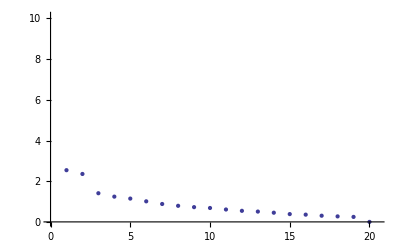

```mathematica
libfile = Import["FormattedCombinatorials_log_ic50.txt","TSV"];
libvals = libfile[[2;;1+ Rows,3;;22]];
rowmeans = Mean[Transpose[libvals]];
rowvariance = StandardDeviation[Transpose[libvals]];
ListPlot[Sort[rowvariance], AxesOrigin->{0,0}]
{StandardDeviation[libvals[[1,All]]], Variance[libvals[[1,All]]]}
MatrixPlot[Transpose[libvals]]
ListPlot[Transpose[libvals]]
For[row = 1, row≤Rows, row++, libvals[[row, All]]=(libvals[[row, All]]-rowmeans[[row]])/rowvariance[[row]];]
{StandardDeviation[libvals[[1,All]]], Variance[libvals[[1,All]]]}
MatrixPlot[Transpose[libvals]]
ListPlot[Transpose[libvals]]
(*By normalizing all rows by their rowmeans, the libvals can be interpreted as deviations of an amino acid from the mean interaction. This makes different rows comparable *) 
Covar2 = Covariance[libvals];
CC2=Correlation[libvals]
{coeigenval2,coeigenvec2}= Eigensystem[Covar2];
Mean[Transpose[coeigenvec2]]
ListPlot[coeigenval2, PlotRange->{{0,20.5},{0,10.1}}]
(*All Eigenvectors have sum = zero, as they are relative differences between amino acids due to the normalization. *)
(*This also means that there is an implied Eigenvector (1,1,1,1...),  of coordinated movements of all amino acids. *)
Max[Covar2 - Transpose[Covar2]];

Covar2 =(Covar2 + Transpose[Covar2]) / 2.0 + .05 ;
(*Adding the transpose ensures exact symmetry, (which due to rounding errors  apparently isn't there even though it should.*) 
(*Adding a constant increases only the Eigenvalue of the Eigenvector (1,1,1,1,1...) to ~ 1.0.  The same effect ccould be achieved by repeating the libvals dataset while adding an offset to all libvals in the repeat. No other eigenvectors are affected. What constant is added is irrelevant for the result. *)
InvCovar2 = Inverse[Covar2] ;
InvCovar2 = (InvCovar2 + Transpose[InvCovar2])/2.0;
Export["InverseCovariance2.txt",InvCovar2,"TSV"];
(* Again, the adding of transpose is to reach perfect symmetry, which should be but isn't the case for the mathematica output (just a difference of 10^-18..., but not nice) *)
```

56

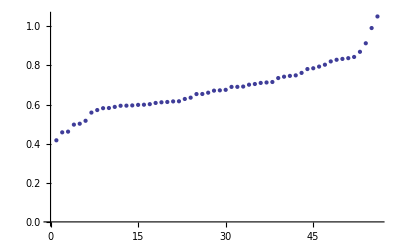

{0.57185,0.327012}

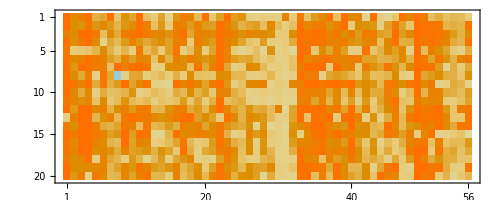

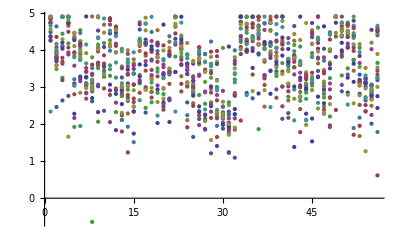

{1.,1.}

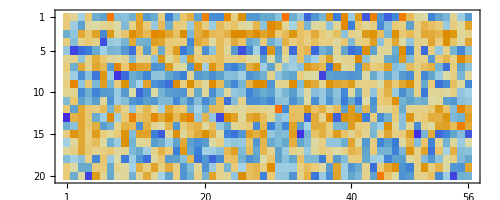

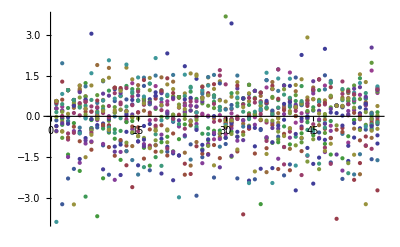

{-9.19403×10^-18,3.64292×10^-18,-3.16587×10^-17,-7.38992×10^-17,9.0726×10^-17,2.36183×10^-16,2.73219×10^-17,-9.19403×10^-18,6.93889×10^-19,5.66821×10^-17,-2.13371×10^-17,-1.73949×10^-16,1.26722×10^-16,1.46844×10^-16,2.77209×10^-16,6.00784×10^-17,-1.6584×10^-16,-2.78206×10^-16,6.64746×10^-16,-0.223607}

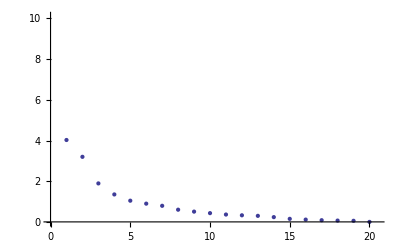

1.11022×10^-16

{{2.51144,-1.17256,0.357857,-1.00663,0.172758,-1.24151,0.505467,-0.180546,0.571167,-0.121114,-0.711024,0.806476,-0.711116,1.78086,-0.819812,-1.0429,-0.235374,-0.387908,2.35864,-0.434169},{-1.17256,5.16126,-0.0820495,-1.21896,0.153959,-1.91445,-0.631052,-0.611218,-0.211033,0.240461,0.597342,-1.21987,-0.13828,1.43664,0.101543,0.68606,0.19857,1.03844,-2.35849,0.943691},{0.357857,-0.0820495,5.60771,-3.54563,-0.269406,0.967227,0.0577986,-0.754263,0.70043,0.838674,-0.0765181,-0.389159,-1.05235,0.533924,-0.668216,-0.608301,-0.659825,0.114664,0.761433,-0.833995},{-1.00663,-1.21896,-3.54563,5.7054,-0.273503,0.970468,-0.0606441,1.01346,-0.240617,-1.46969,0.324164,0.843216,0.97911,-2.39336,1.0512,0.141653,0.791879,-0.137342,-1.00874,0.534573},{0.172758,0.153959,-0.269406,-0.273503,1.52126,-1.43963,-0.358931,-0.0630055,0.22397,-0.545127,0.116158,-0.31686,0.125064,1.22493,-0.102656,0.612904,-0.000515468,0.398808,-0.295267,0.115089},{-1.24151,-1.91445,0.967227,0.970468,-1.43963,7.22254,0.891754,0.0380338,-0.481376,1.04297,0.346854,0.850897,0.489224,-4.03287,0.806209,-1.64822,0.721889,-1.41867,0.0844857,-1.25582},{0.505467,-0.631052,0.0577986,-0.0606441,-0.358931,0.891754,2.2191,0.240459,-0.229845,-0.186216,-0.287607,0.0961796,0.0404433,0.062446,-0.443814,-1.04322,-0.0341954,0.232676,0.245251,-0.316055},{-0.180546,-0.611218,-0.754263,1.01346,-0.0630055,0.0380338,0.240459,2.71455,-0.407669,-0.718269,0.0258356,0.0975376,0.471211,-0.441238,0.492233,0.384227,0.488263,-1.31496,-0.814122,0.339491},{0.571167,-0.211033,0.70043,-0.240617,0.22397,-0.481376,-0.229845,-0.407669,2.73176,-1.0196,-0.235279,0.31293,-0.294006,1.19942,-1.49529,-1.80222,1.14341,-0.302894,1.0345,-0.197743},{-0.121114,0.240461,0.838674,-1.46969,-0.545127,1.04297,-0.186216,-0.718269,-1.0196,5.24889,-1.22409,-0.282106,0.208024,-1.70823,0.612793,2.04288,-0.84617,-1.4609,0.608101,-0.261285},{-0.711024,0.597342,-0.0765181,0.324164,0.116158,0.346854,-0.287607,0.0258356,-0.235279,-1.22409,3.45386,-0.332259,0.748577,-1.02282,0.415751,-0.250091,0.636587,0.138196,-1.54696,-0.116686},{0.806476,-1.21987,-0.389159,0.843216,-0.31686,0.850897,0.0961796,0.0975376,0.31293,-0.282106,-0.332259,3.28873,0.123155,-1.10896,0.18726,-2.38414,1.53834,-1.03214,0.439331,-0.518546},{-0.711116,-0.13828,-1.05235,0.97911,0.125064,0.489224,0.0404433,0.471211,-0.294006,0.208024,0.748577,0.123155,1.49982,-1.34006,0.416715,0.5179,0.289723,-0.692767,-0.946931,0.266543},{1.78086,1.43664,0.533924,-2.39336,1.22493,-4.03287,0.062446,-0.441238,1.19942,-1.70823,-1.02282,-1.10896,-1.34006,6.32294,-1.60239,-0.788163,-0.651695,1.74001,1.19393,0.594699},{-0.819812,0.101543,-0.668216,1.0512,-0.102656,0.806209,-0.443814,0.492233,-1.49529,0.612793,0.415751,0.18726,0.416715,-1.60239,2.0426,0.55815,0.221011,0.0820099,-0.937074,0.0817712},{-1.0429,0.68606,-0.608301,0.141653,0.612904,-1.64822,-1.04322,0.384227,-1.80222,2.04288,-0.250091,-2.38414,0.5179,-0.788163,0.55815,9.79419,-6.28795,1.64167,-0.768025,1.2436},{-0.235374,0.19857,-0.659825,0.791879,-0.000515468,0.721889,-0.0341954,0.488263,1.14341,-0.84617,0.636587,1.53834,0.289723,-0.651695,0.221011,-6.28795,7.60968,-2.90717,-0.680968,-0.335491},{-0.387908,1.03844,0.114664,-0.137342,0.398808,-1.41867,0.232676,-1.31496,-0.302894,-1.4609,0.138196,-1.03214,-0.692767,1.74001,0.0820099,1.64167,-2.90717,5.0122,-0.409707,0.665795},{2.35864,-2.35849,0.761433,-1.00874,-0.295267,0.0844857,0.245251,-0.814122,1.0345,0.608101,-1.54696,0.439331,-0.946931,1.19393,-0.937074,-0.768025,-0.680968,-0.409707,5.48,-1.43938},{-0.434169,0.943691,-0.833995,0.534573,0.115089,-1.25582,-0.316055,0.339491,-0.197743,-0.261285,-0.116686,-0.518546,0.266543,0.594699,0.0817712,1.2436,-0.335491,0.665795,-1.43938,1.92392}}

InverseCovariance3.txt

```mathematica
(*By normalizing all rows by their rowmeans, the libvals can be interpreted as deviations of an amino acid from the mean interaction. This makes different rows comparable *) 
libfile2 = Import["FormattedCombinatorials_log_ic50_min_hundredfold_difference.txt","TSV"];
Rows2 = Dimensions[libfile2][[1]]-1
libvals2 = libfile2[[2;;1+ Rows2,3;;22]];
rowmeans = Mean[Transpose[libvals2]];
rowvariance = StandardDeviation[Transpose[libvals2]];
ListPlot[Sort[rowvariance], AxesOrigin->{0,0}]
{StandardDeviation[libvals2[[1,All]]], Variance[libvals2[[1,All]]]}
MatrixPlot[Transpose[libvals2]]
ListPlot[Transpose[libvals2], PlotRange-> All]
For[row = 1, row≤Rows2, row++, libvals2[[row, All]]=(libvals2[[row, All]]-rowmeans[[row]])/rowvariance[[row]];]
{StandardDeviation[libvals2[[1,All]]], Variance[libvals2[[1,All]]]}
MatrixPlot[Transpose[libvals2]]
ListPlot[Transpose[libvals2]]
Covar3 = Covariance[libvals2];
CC3=Correlation[libvals2];
{coeigenval3,coeigenvec3}= Eigensystem[Covar3];
Mean[Transpose[coeigenvec3]]
ListPlot[coeigenval3, PlotRange->{{0,20.5},{0,10.1}}]
(*All Eigenvectors have sum = zero, as they are relative differences between amino acids due to the normalization. *)
(*This also means that there is an implied Eigenvector (1,1,1,1...),  of coordinated movements of all amino acids. *)
Max[Covar3 - Transpose[Covar3]]
Covar3 =(Covar3 + Transpose[Covar3]) / 2.0 + .05 ;
(*Adding the transpose ensures exact symmetry, (which due to rounding errors  apparently isn't there even though it should.*) 
(*Adding a constant increases only the Eigenvalue of the Eigenvector (1,1,1,1,1...) to ~ 1.0.  The same effect ccould be achieved by repeating the libvals dataset while adding an offset to all libvals in the repeat. No other eigenvectors are affected. What constant is added is irrelevant for the result. *)
InvCovar3 = Inverse[Covar3] ;
InvCovar3 = (InvCovar3 + Transpose[InvCovar3])/2.0
Export["InverseCovariance3.txt",InvCovar3,"TSV"]
```

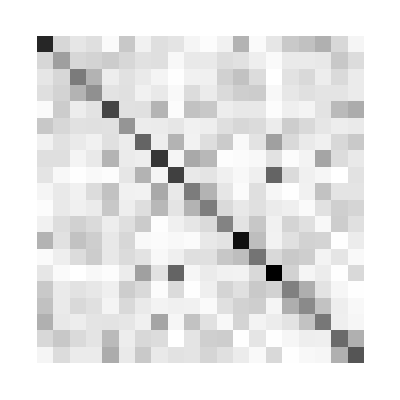
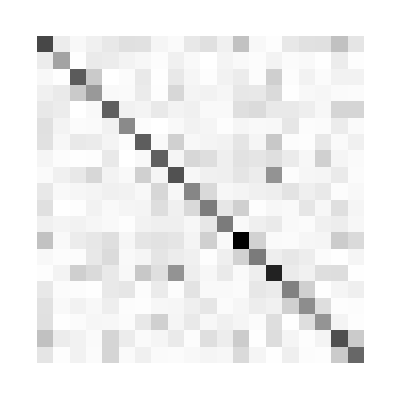
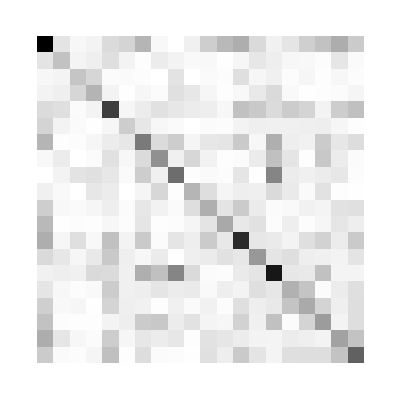

{-0.0591662,-0.36243,-0.598388}

{0.383623,1.49387,1.8626}

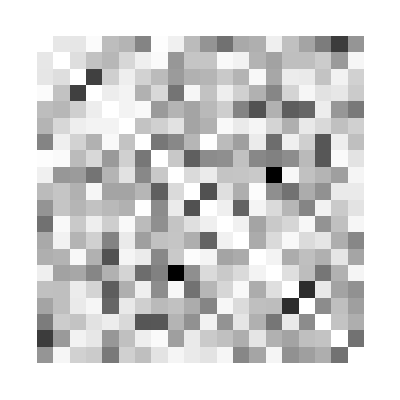
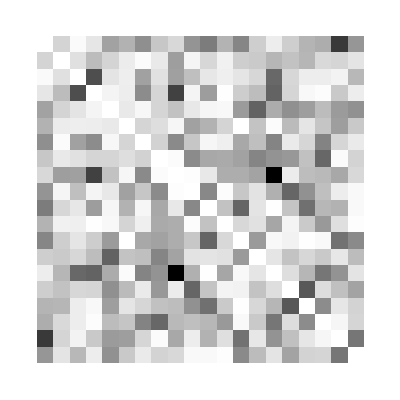
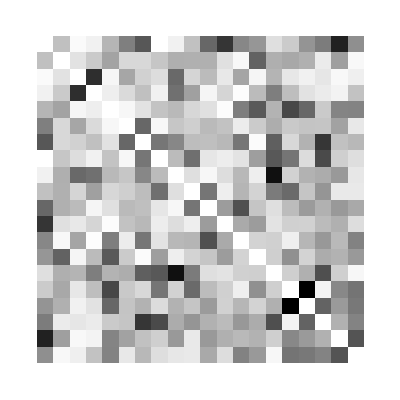

{-0.497215,-0.411154,-0.605656}

{0.65099,0.529607,0.69442}

```mathematica
{ArrayPlot[Covar], ArrayPlot[Covar2], ArrayPlot[Covar3]}
{Min[Covar], Min[Covar2], Min[Covar3]}
{Max[Covar], Max[Covar2], Max[Covar3]}
For[i=1, i<=20, i++, CC[[i,i]]=0; CC2[[i,i]]=0; CC3[[i,i]]=0]
{ArrayPlot[CC], ArrayPlot[CC2], ArrayPlot[CC3]}
{Min[CC], Min[CC2], Min[CC3]}
{Max[CC], Max[CC2], Max[CC3]}
```

```mathematica
SMM - BP
```

```mathematica
(*Import experimental data*)
expfile=Import["mathematica-peptides.csv","CSV"];
H = expfile[[All, 1;;181]];
ineq = expfile[[All, 182]];
meas = expfile[[All, 183]];
Dimensions[meas]
```

{231}

0.316386

{180,180}

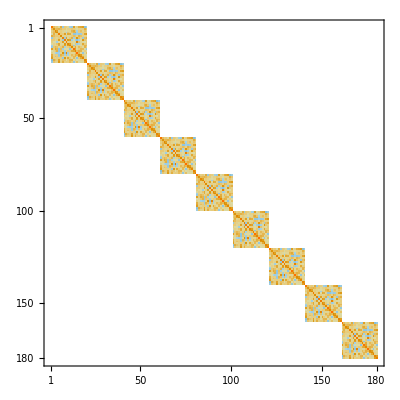
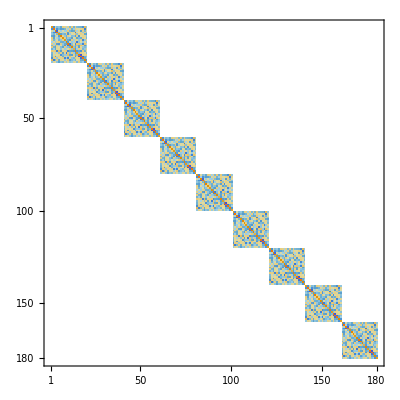

{181,181}

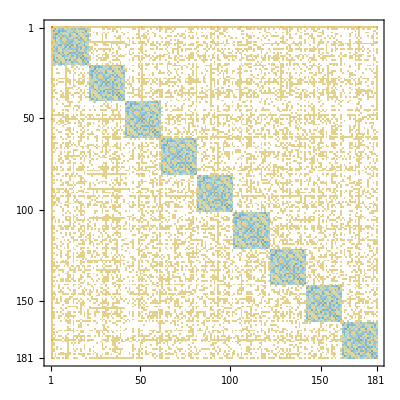

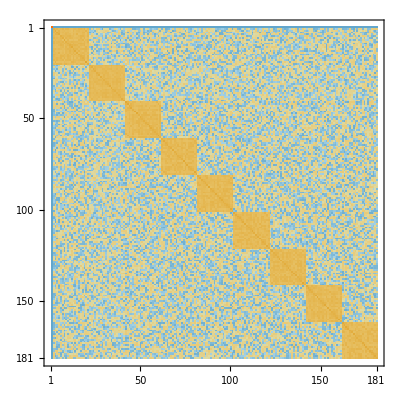

{1.96619,-0.547932,0.0643044,0.0326423,0.231396,0.319533,-0.0107652,-0.052259,-0.185035,-0.141761,-0.0403271,-0.502873,-0.215895,0.927969,0.147312,-0.409926,-0.0779054,-0.0504079,0.0167316,0.212502,0.282695,-0.285154,-0.138455,0.118468,0.169989,0.0114773,0.437766,0.0194631,0.0321737,-0.11656,0.293396,-0.177579,0.0930101,1.1236,-0.13549,-0.505924,-0.0541759,-0.0330854,-0.2807,-0.458191,-0.114032,0.252967,0.0350579,0.606631,0.615599,-0.657749,0.532053,-0.584451,-0.480511,0.157291,0.0878357,-0.466614,0.36464,1.00462,0.413081,-0.154346,0.32384,-0.35371,-0.354088,-0.65451,-0.687643,-0.126259,0.174158,-0.676383,-0.0223867,0.0456618,0.400906,0.225822,0.257048,0.0570699,0.251618,0.229454,-0.129337,0.321313,0.0910535,-0.205804,-0.0632505,-0.111837,-0.00220861,-0.687865,-0.0287735,0.151212,0.0480509,0.301865,0.117118,-0.518676,0.419868,-0.129837,-0.206679,0.214446,-0.0467505,-0.0213348,0.245143,0.0252211,0.0518906,0.1059,0.0392967,0.148868,-0.107803,-0.561792,-0.276007,-0.19086,-0.0961792,0.174021,0.482519,-0.111803,-0.104026,-0.447361,-0.0692637,0.380399,-0.073876,-0.000404175,-0.105863,0.176382,0.274998,0.17832,0.0455721,0.151604,-0.0624759,-0.358908,-0.242796,0.131573,-0.329891,0.198328,-0.0364095,-0.314907,0.0839755,-0.107921,-0.0184824,0.934384,-0.0719359,-0.195537,0.00792585,-0.00578697,-0.257027,0.0296687,0.0386268,0.371486,0.39469,-0.291359,-0.5614,0.398095,-0.343343,0.00672422,0.120139,-0.388455,0.287439,-0.430398,-0.0319156,0.226034,0.329368,-0.20508,0.0484945,0.339636,0.317465,-0.244918,0.0282694,0.14456,0.38301,-0.361415,-0.623709,0.436207,-0.409339,1.05237,1.01504,-1.3042,1.00532,0.026277,-0.748966,1.03959,-0.729936,-1.24837,0.0220105,-0.292349,0.0575107,0.981825,0.742232,0.496058,-0.16684,-0.978068,-0.996376}

{0,2,21,-1.99007×10^-13}

{1,22,41,1.58346×10^-13}

{2,42,61,1.51545×10^-13}

{3,62,81,-2.84526×10^-13}

{4,82,101,-1.60816×10^-13}

{5,102,121,3.99708×10^-13}

{6,122,141,-5.51559×10^-13}

{7,142,161,-1.35225×10^-13}

{8,162,181,-2.5524×10^-13}

```mathematica
(*construct covariance matrix for 9-ner peptides*)
lambda= Sqrt[.1001] (* lambda =  standard deviation of the error distribution *)
c= Table[0,{i,180},{j,180}];
Dimensions[c]
For[pos=0, pos<9, pos++, c[[1+pos*20;;20+pos*20,1+pos*20;;20+pos*20]]=Covar;];
cinverse = Inverse[c] *lambda^2;
{MatrixPlot[c], MatrixPlot[cinverse] }
(* now construct the analytical solution of SMM-BP for the peptides, measurements covariance and lambda given *) 
minv = Transpose[H].H;
Dimensions[minv]
minv[[2;;181,2;;181]]+=cinverse;
MatrixPlot[minv]
minvinv=Inverse[minv];
MatrixPlot[minvinv]
y= minvinv.Transpose[H].meas
For[i=0, i<9, i++, Print[{i,2+i*20, 1+(i+1)*20 ,Sum[y[[j]],{j,2+i*20, 1+(i+1)*20}]}]]
(* The  solutions have sum 0 at each position*)
```

```mathematica
(* Compare the results if a constant offset is added to the Covariance matrix *)
c2= Table[0,{i,180},{j,180}];
For[pos=0, pos<9, pos++, c2[[1+pos*20;;20+pos*20,1+pos*20;;20+pos*20]]=Covar + 10;];
cinverse2 = Inverse[c2] *lambda^2;
minv2 = Transpose[H].H;
minv2[[2;;181,2;;181]]+=cinverse2;
minvinv2=Inverse[minv2];
y2= minvinv2.Transpose[H].meas
Max[Abs[y - y2]]
Max[Abs[minvinv2-minvinv]]
(* Should show no difference in the solution but in the mininv *)
```

{1.96619,-0.547932,0.0643044,0.0326423,0.231396,0.319533,-0.0107652,-0.052259,-0.185035,-0.141761,-0.0403271,-0.502873,-0.215895,0.927969,0.147312,-0.409926,-0.0779054,-0.0504079,0.0167316,0.212502,0.282695,-0.285154,-0.138455,0.118468,0.169989,0.0114773,0.437766,0.0194631,0.0321737,-0.11656,0.293396,-0.177579,0.0930101,1.1236,-0.13549,-0.505924,-0.0541759,-0.0330854,-0.2807,-0.458191,-0.114032,0.252967,0.0350579,0.606631,0.615599,-0.657749,0.532053,-0.584451,-0.480511,0.157291,0.0878357,-0.466614,0.36464,1.00462,0.413081,-0.154346,0.32384,-0.35371,-0.354088,-0.65451,-0.687643,-0.126259,0.174158,-0.676383,-0.0223867,0.0456618,0.400906,0.225822,0.257048,0.0570699,0.251618,0.229454,-0.129337,0.321313,0.0910535,-0.205804,-0.0632505,-0.111837,-0.00220861,-0.687865,-0.0287735,0.151212,0.0480509,0.301865,0.117118,-0.518676,0.419868,-0.129837,-0.206679,0.214446,-0.0467505,-0.0213348,0.245143,0.0252211,0.0518906,0.1059,0.0392967,0.148868,-0.107803,-0.561792,-0.276007,-0.19086,-0.0961792,0.174021,0.482519,-0.111803,-0.104026,-0.447361,-0.0692637,0.380399,-0.073876,-0.000404175,-0.105863,0.176382,0.274998,0.17832,0.0455721,0.151604,-0.0624759,-0.358908,-0.242796,0.131573,-0.329891,0.198328,-0.0364095,-0.314907,0.0839755,-0.107921,-0.0184824,0.934384,-0.0719359,-0.195537,0.00792585,-0.00578697,-0.257027,0.0296687,0.0386268,0.371486,0.39469,-0.291359,-0.5614,0.398095,-0.343343,0.00672422,0.120139,-0.388455,0.287439,-0.430398,-0.0319156,0.226034,0.329368,-0.20508,0.0484945,0.339636,0.317465,-0.244918,0.0282694,0.14456,0.38301,-0.361415,-0.623709,0.436207,-0.409339,1.05237,1.01504,-1.3042,1.00532,0.026277,-0.748966,1.03959,-0.729936,-1.24837,0.0220105,-0.292349,0.0575107,0.981825,0.742232,0.496058,-0.16684,-0.978068,-0.996376}

4.41582×10^-11

899.101

```mathematica
SolveCoSMM[Peptides_, meas_, sigma_]:=
Module[{W, error,ExpFit,PCov, CoSMM, N}, 
W:= Table[Subscript[w, i],{i,181}];
error = Peptides.W- meas;
N = Dimensions[meas][[1]];
ExpFit= Product[PDF[NormalDistribution[0,sigma], error[[i]]],{i,1,N}];
PCov[x_]:=PDF[MultinormalDistribution[Table[0,{i,20}],Covar],x];
CoSMM[x_]:=Product[PCov[x[[2+20*pos;;21+20*pos]]],{pos,0,8}];
Maximize[(ExpFit * CoSMM[W]) , W]
]
SetSplit[Peptides_, meas_, cv_Integer, cvNum_Integer]:=
Module[{trainpep, trainmeas, blindpep, blindmeas,N,i},
N = Dimensions[meas][[1]];
trainpep={};
trainmeas = {};
blindpep={};
blindmeas = {};
For[i=1, i<=N, i++,
If[ Mod[(i-1),cvNum]==cv,
AppendTo[blindpep,Peptides[[i]]];AppendTo[blindmeas,meas[[i]]];, 
AppendTo[trainpep,Peptides[[i]]];AppendTo[trainmeas,meas[[i]]];]];
{trainpep, trainmeas, blindpep, blindmeas}
]
crossValidate[Peptides_,meas_,sigma_,cvNum_Integer]:=
Module[{cv, t, tm, b, bm, sol,W, p,pred, x},
pred ={}; 
x={};
W:= Table[Subscript[w, i],{i,181}];
For[cv=0, cv<cvNum, cv++,
{t, tm, b, bm}=SetSplit[Peptides,meas,cv,cvNum];
PrintTemporary[cv];sol=SolveCoSMM[t,tm,sigma];
p = b.(W/.sol[[2]]);
pred=Join[pred,p];
x=Join[x,bm];
];
{x,pred}
]
optimalSigma[Peptides_,meas_,smin_,smax_,sstep_, cvNum_Integer]:=
Module[{p,m, corr, dist, sigma,s, vals},
corr ={};
dist = {};
sigma = {};
vals ={};
For[s=smin, s<smax, s*=sstep,
{m,p} = crossValidate[Peptides,meas,s,cvNum];
sigma=Append[sigma,s];
vals=Append[vals,{m,p}];
corr=Append[corr, Correlation[m,p] * Correlation[m,p]];
dist=Append[dist,(m-p).(m-p)];
Print[sigma,corr,dist];
];
]
```

```mathematica
x = SolveCoSMM[H,meas,lambda];
W:= Table[Subscript[w, i],{i,181}];
y2 = W /. x[[2]];
Max[Abs[y - y2]] (* Evaluates how far the numerical is from the analytical solution *)
```

3.9746×10^-13

```mathematica
(*Run Cross Validation on this, determine optimal Lambda, compare to CPP solution *)
CPPlambda = Sqrt[0.264305]
optimalSigma[H,meas,CPPlambda,1,10,5]
```

0.514106

{0.514106}{0.540641}{121.213}

```mathematica
optimalSigma[H,meas,0.1,1,2,5]
optimalSigma[H,meas,CPPlambda,1,10,5]
optimalSigma[H,meas,CPPlambda+0.01,1,10,5]
optimalSigma[H,meas,CPPlambda-0.01,1,10,5]
```

```mathematica
(* Redo the functions to include position specific lambda, for convencience and confusion, use lambda, not lambda^2 *)
SolveCoSMM2[Peptides_, meas_, sigma_]:=
Module[{W, error,ExpFit,PCov, CoSMM, N}, 
W:= Table[Subscript[w, i],{i,181}];
error = Peptides.W- meas;
N = Dimensions[meas][[1]];
ExpFit= Product[PDF[NormalDistribution[0,1], error[[i]]],{i,1,N}];
PCov[x_, l_]:=PDF[MultinormalDistribution[Table[0,{i,20}], l^-2 * Covar],x];
CoSMM[x_]:=Product[
PDF[ MultinormalDistribution[ Table[0,{i,20}] , sigma[[pos+1]]^-2 * Covar], x[[2+20*pos;;21+20*pos]]]
,{pos,0,8}];
Maximize[(ExpFit * CoSMM[W]) , W]
]
crossValidate2[Peptides_,meas_,sigma_,cvNum_Integer]:=
Module[{cv, t, tm, b, bm, sol,W, p,pred, x, dist},
pred ={}; 
x={};
W:= Table[Subscript[w, i],{i,181}];
For[cv=0, cv<cvNum, cv++,
PrintTemporary[{"CV", cv}];
{t, tm, b, bm}=SetSplit[Peptides,meas,cv,cvNum];
sol=SolveCoSMM2[t,tm,sigma];
p = b.(W/.sol[[2]]);
pred=Join[pred,p];
x=Join[x,bm];
];
dist = ((x-pred).(x-pred)) / Length[x]
]
Distance2[sigma_]:= crossValidate2[H,meas,sigma,5]
```

```mathematica
l = Table[CPPlambda,{i,9}]
Distance2[l]
```

{0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106,0.514106}

0.52473

```mathematica
For[pos=1, pos≤9, pos++, 
l2=l;
l2[[pos]]+=0.001;
d2 = Distance2[l2];
Print[(d2-0.52473)/0.001];
]
```

-0.0686885

0.0452462

0.0156438

0.0285112

-0.0581824

-0.0250599

-0.0683745

-0.081171

0.216083

```mathematica
lopt={0.561222,0.155626,0.32379,0.166698,1.12112,0.251857,2.99055,0.777421,0.080459};
Distance2[Sqrt[lopt]]
```

0.441571

```mathematica
(*Gradient at optimum*)
For[pos=1, pos≤9, pos++, 
l2=Sqrt[lopt];
l2[[pos]]+=0.001;
d2 = Distance2[l2];
Print[{d2, (d2-0.44157149072845525)/0.001}];
]
```

{0.441572,0.0000923039}

{0.441572,0.000104651}

{0.441572,0.00010551}

{0.441572,0.0000172368}

{0.441572,0.0000142444}

{0.441572,0.0000382668}

{0.441571,-0.0000121942}

{0.441572,0.0000158253}

{0.441572,0.000488736}